# MGDrivE: Split Drive

```mathematica
(*Set the path for the experiments*)
(*{USER,DRIVE,PAR}={3,1,1};
If[PAR==1,
If[DRIVE==1,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/SplitDrive/2018_11_27_GARBAGE"]];
If[DRIVE==2,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/InundativeRelease/2018_11_27_GARBAGE"]];
If[DRIVE==3,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/CRISPR/2018_11_27_GARBAGE"]];
exp="_02_098_098_";,
If[DRIVE==1,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/SD_BioParams/SplitDrive/2018_11_30_GARBAGE"]];
If[DRIVE==2,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/SD_BioParams/InundativeRelease/2018_11_30_GARBAGE"]];
If[DRIVE==3,SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/SD_BioParams/CRISPR/2018_11_30_GARBAGE"]];
exp="_05_079_076_";
]*)
```

```mathematica
DRIVE =3;
exp="_04_061_070_";
If[DRIVE==1,SetDirectory["/Volumes/marshallShare/SplitDrive_Sweep/SplitDrive/2019_03_14_GARBAGE/"]]
If[DRIVE==2,SetDirectory["/Volumes/marshallShare/SplitDrive_Sweep/InundativeRelease/2019_03_14_GARBAGE/"]]
If[DRIVE==3,SetDirectory["/Volumes/marshallShare/SplitDrive_Sweep/CRISPR/2019_03_14_GARBAGE/"]]
```

/Volumes/marshallShare/SplitDrive_Sweep/CRISPR/2019_03_14_GARBAGE

## Ecology

0) Genotypes

```mathematica
If[DRIVE==1||DRIVE==2,
genotypesGroups={
{{02,05,05,06,07,12,15,15,16,17,22,25,25,26,27},"H"},
{{04,07,09,10,10,14,17,19,20,20,24,27,29,30,30},"B"},
{{03,06,08,08,09,13,16,18,18,19,23,26,28,28,29},"R"},
{{01,01,02,03,04,11,11,12,13,14,21,21,22,23,24},"W"},
{{11,12,13,14,15,16,17,18,19,20,21,21,22,22,23,23,24,24,25,25,26,26,27,27,28,28,29,29,30,30},"C"}
};
modifier=1;
{rs,releases,ri}={20,10,7};
ecoIndex=4;
]
If[DRIVE==3,
genotypesGroups={
{{02,05,05,06,07},"H"},
{{04,07,09,10,10},"B"},
{{03,06,08,08,09},"R"},
{{01,02,02,03,04},"W"}
};
modifier=1;
{rs,releases,ri}={20,1,7};
]
(*Define genotypes colors*)
originalColorsValues={
{0,100,70,0},
{50,0,50,0},
{60,100,0,0},
{10,100,0,0},
{30,20,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
Transpose[{Append[rgbColors,RGBColor[0., 0.25, 0.75]],Append[genotypesGroups[[All,2]],"Total"]}]//Grid
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Grid[Transpose[{{RGBColor[1., 0., 0.30000000000000004],RGBColor[0.5, 1., 0.5],RGBColor[0.4, 0., 1.],RGBColor[0.9, 0., 1.],RGBColor[0.7, 0.8, 1.],RGBColor[0., 0.25, 0.75]},{H,B,R,W,Total}}]]

1) Functions

```mathematica
PlotLineDynamics[aggregatedGroupData_,genotypeIndex_,rgbaColors_,{opacity_,thickness_},plotRange_,lines_]:=ListLinePlot[
aggregatedGroupData[[All,All,genotypeIndex]]
,AspectRatio->1/4
,Frame->True
(*,FrameLabel->(Style[#,175]&/@{"Time","Female Mosquitos"})*)
,FrameTicks->{{{{.25,"0.25 "},{.5,"0.50 "},{.75,"0.75 "},{1,"1.00 "}},None},{Range[0,1500,250],None}}
,FrameTicksStyle->100
,FrameStyle->Thickness[.002]
,GridLines->{Range[0,1500,250],Range[.25,1,.25]}
,GridLinesStyle->Directive[Gray,Thickness[.001],Opacity[.35]]
,ImageSize->1500
,ImagePadding->Automatic
,InterpolationOrder->1
,PlotRange->plotRange
,PlotRangePadding->0
,PlotStyle->Directive[rgbaColors[[genotypeIndex]],Thickness[thickness],Opacity[opacity]]
,Epilog->{Opacity[.2],Black,Thickness[.001],lines}
]
PlotLineDynamicsBatch[aggregatedGroupData_,genotypeIndex_,rgbaColors_,{opacity_,thickness_},plotRange_,lines_]:=ListLinePlot[
aggregatedGroupData[[All,All,genotypeIndex]]
,AspectRatio->1/4
,Background->Black
,Frame->True
(*,FrameLabel->(Style[#,175]&/@{"Time","Female Mosquitos"})*)
,FrameTicks->None
,FrameStyle->Thickness[Directive[Thickness[.002],White]]
,ImageSize->2000
,ImagePadding->Automatic
,InterpolationOrder->1
,PlotRange->plotRange
,PlotRangePadding->0
,PlotStyle->Directive[rgbaColors[[genotypeIndex]],Thickness[thickness],Opacity[opacity]]
,Epilog->{Opacity[1],White,Thickness[.00025],lines}
]
```

### Plots

```mathematica
GenerateMatrixPlotsNonNormalized[aggregatedGroupData_,timeRange_,maxesMax_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
GenerateStreamChart[counts_]:=BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
,GridLines->{Range[0,50000,100],Range[0,1.5*counts//Flatten//Max,100]}
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
GenerateMatrixPlotsSplits[matrixPlots_]:=GraphicsGrid[Prepend[
Transpose[{Show[#,FrameTicks->None]&/@matrixPlots}],
{Show[matrixPlots,FrameTicks->None]}
]]
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateMatrixPlots[aggregatedGroupData_,timeRange_,maxesMax_,rgbaColors_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
```

### Data

```mathematica
AggregateByGenotype[rawDataTotal_,genotypesGroups_]:=Module[{aggregatedData,outputTotals,totals,transposedTotals},
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
transposedTotals
]

GetMaxPopulation[aggregatedGroupData_,genotypesGroups_,timeRange_]:=Module[{i,maxes,genotypeA,genotypeAtemp,maxesMax},
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
maxesMax
]

FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
CalculateCounts[aggregatedGroupData_,genotypesGroups_]:=Module[{genotypeTemp,genotypeTotal},
Table[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}]
]
ImportExperimentRawData[experimentString_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Patch*","AF1_Aggregate_Patch*"};(*CHANGE TO AF1*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
ImportExperimentRawDataByNode[experimentString_,nodePattern_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Patch"<>nodePattern<>".csv","AF1_Aggregate_Patch"<>nodePattern<>".csv"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=(*rawDataMale+*)rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
CalculateGenotypesGroups[genotypes_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=StringPartition[#,1]&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
CalculateGenotypesGroupsOnLocus[genotypes_,locusRange_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=(StringPartition[#,1][[locusRange[[1]];;locusRange[[2]]]])&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
```

2) Single Experiment Dynamics

```mathematica
xRange=Range[rs,(releases*ri+rs)-1,ri];
lines={Line[{{#,0},{#,10000}}]&/@xRange,Null};
nodes={"0000","0001"};
Table[
experimentString="E_0"<>ToString[DRIVE]<>exp<>StringPadLeft[ToString[releases],2,"0"]<>"_10000";
nodePattern=nodes[[i]];
tempLoad=ImportExperimentRawDataByNode[experimentString,nodePattern];
{rawDataExperiments,genotypes}={tempLoad[[1]],tempLoad[[2]]};
genotypes;
aggregatedGroupData=AggregateByGenotype[#,genotypesGroups][[1]]&/@rawDataExperiments;
maxPopSize=aggregatedGroupData//Flatten//Max;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
genotypesGroups//Grid;
aggregatedGroupDataWithTotal=Table[
sampled=aggregatedGroupData[[i]];
normalizingTotals=Total/@sampled[[All,1;;4]];
sampled/normalizingTotals//N
,{i,1,aggregatedGroupData//Length}];
(**)
popDyns=Table[
PlotLineDynamics[aggregatedGroupDataWithTotal,j,Append[rgbaColors,{Lighter[RGBColor[0., 0.25, 0.75],0],Lighter[RGBColor[0., 0.25, 0.75],0]}],{.65,.0001},{{0,1500},{0,1}},lines[[i]]]
,{j,1,(genotypesGroups//Length)}]//Show;
Export["../../images/E"<>experimentString<>"_N"<>nodePattern<>".png",popDyns,ImageSize->5000]
,{i,1,2}]
sw=SwatchLegend[rgbColors,genotypesGroups[[All,2]]
,LabelStyle->30
,LegendMarkerSize->25
];
Export["../../images/"<>"E0_ColorSwatch.png",sw,ImageResolution->500];
```

{../../images/EE_03_04_061_070_01_10000_N0000.png,../../images/EE_03_04_061_070_01_10000_N0001.png}

2) Single Experiment Dynamics (explore)

```mathematica
exp="_04_098_098_";
(**) 
xRange=Range[rs,(releases*ri+rs)-1,ri];
lines={Line[{{#,0},{#,10000}}]&/@xRange,Null};
nodes={"0000","0001"};
Table[
experimentString="E_0"<>ToString[DRIVE]<>exp<>StringPadLeft[ToString[releases],2,"0"]<>"_10000";
nodePattern=nodes[[i]];
tempLoad=ImportExperimentRawDataByNode[experimentString,nodePattern];
{rawDataExperiments,genotypes}={tempLoad[[1]],tempLoad[[2]]};
genotypes;
aggregatedGroupData=AggregateByGenotype[#,genotypesGroups][[1]]&/@rawDataExperiments;
maxPopSize=aggregatedGroupData//Flatten//Max;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
genotypesGroups//Grid;
aggregatedGroupDataWithTotal=Table[
totals=(Total/@aggregatedGroupData[[i]]);
Transpose[Append[aggregatedGroupData[[i]]//Transpose,totals]]
,{i,1,aggregatedGroupData//Length}];
(**)
popDyns=Table[
PlotLineDynamics[aggregatedGroupDataWithTotal,j,Append[rgbaColors,{Lighter[RGBColor[0., 0.25, 0.75],0],Lighter[RGBColor[0., 0.25, 0.75],0]}],{.5,.00008},{{0,1500},{0,6000}},lines[[i]]]
,{j,1,(genotypesGroups//Length)+1}]//Show;
Export["./00_images/H"<>experimentString<>"_N"<>nodePattern<>".png",popDyns,ImageSize->5000]
,{i,1,1}]
```

{./00_images/HE_03_04_098_098_01_10000_N0000.png}

```mathematica
threshold=.8
totals=aggregatedGroupDataWithTotal[[All,All,3]];
drive=aggregatedGroupDataWithTotal[[All,All,1]];
(**)
ratios=drive/totals;
outs=Table[
suppressionDays=Position[(threshold<#)&/@i,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>Last[xRange]];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-Last[xRange];
{fitGRNA,femHoming,releasesNum,suppressionTime}
,{i,ratios}];
outs[[All,4]]//Median//N
```

0.8

Median[{}]

3) Batch Experiment Dynamics

```mathematica
experiments=FileNames["E_*",Directory[]];
Table[
nodes={"0000","0001"};
Table[
experimentString=(StringSplit[k,"/"]//Last);
releases=StringSplit[experimentString,"_"][[-2]]//ToExpression;
xRange=Range[rs,(releases*ri+rs)-1,ri];
lines={Line[{{#,0},{#,10000}}]&/@xRange,Null};
nodePattern=nodes[[i]];
tempLoad=ImportExperimentRawDataByNode[experimentString,nodePattern];
{rawDataExperiments,genotypes}={tempLoad[[1]],tempLoad[[2]]};
genotypes;
aggregatedGroupData=AggregateByGenotype[#,genotypesGroups][[1]]&/@rawDataExperiments;
maxPopSize=aggregatedGroupData//Flatten//Max;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
genotypesGroups//Grid;
aggregatedGroupDataWithTotal=Table[
sampled=aggregatedGroupData[[i]];
normalizingTotals=Total/@sampled[[All,1;;4]];
sampled/normalizingTotals//N
,{i,1,aggregatedGroupData//Length}];
(**)
popDyns=Table[
PlotLineDynamics[aggregatedGroupDataWithTotal,j,Append[rgbaColors,{Lighter[RGBColor[0., 0.25, 0.75],0],Lighter[RGBColor[0., 0.25, 0.75],0]}],{.75,.0001},{{0,1500},{0,1}},lines[[i]]]
,{j,1,(genotypesGroups//Length)}]//Show;
Export["./00_images/E"<>experimentString<>"_N"<>nodePattern<>".png",popDyns,ImageSize->5000]
,{i,1,2}]
,{k,experiments}];

sw=SwatchLegend[Append[rgbColors,RGBColor[0., 0.25, 0.75]],Append[genotypesGroups[[All,2]],"Total"]
,LabelStyle->30
,LegendMarkerSize->25
];
Export["./00_images/"<>"00E_ColorSwatch.png",sw,ImageResolution->500];
```

Part::take: Cannot take positions 1 through 4 in {0,5039}.

Total::normal: Nonatomic expression expected at position 1 in Total[All].

Part::pkspec1: The expression Total[All] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 4 in {0,5021}.

Total::normal: Nonatomic expression expected at position 1 in Total[All].

Part::take: Cannot take positions 1 through 4 in {0,5003}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[All].

General::stop: Further output of Total::normal will be suppressed during this calculation.

$Aborted

$Aborted

4) Collage

```mathematica
(*files=FileNames["A*.png",Directory[]<>"/00_images/"];
images=ImageRotate[ImageResize[Import[#],1000],0Degree]&/@files;
Export["00_animation.gif",images,ImageSize->1000,Background->Black]*)
```

5) Ad hoc Number Analysis

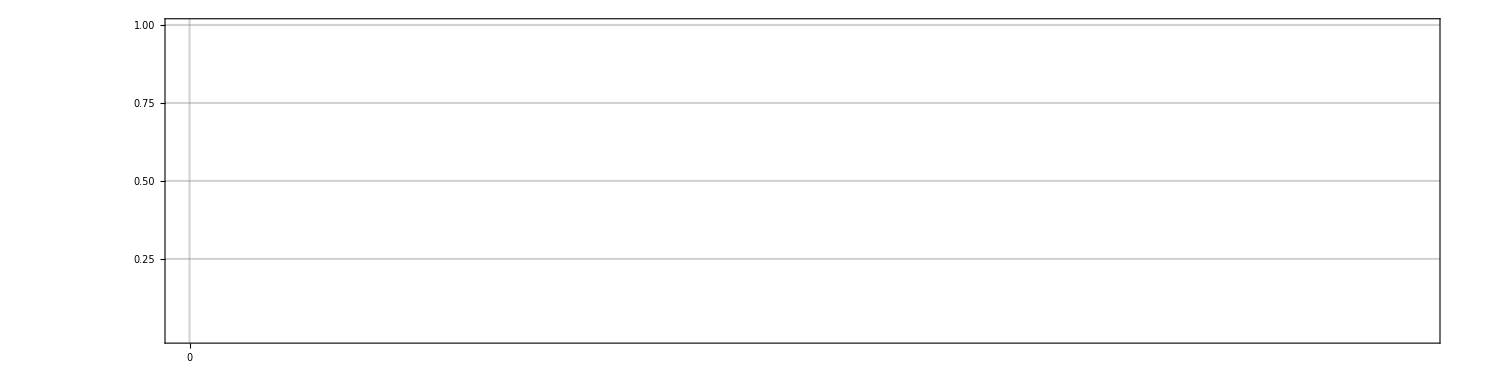

```mathematica
xRange=Range[rs,(releases*ri+rs)-1,ri];
lines={Line[{{#,0},{#,10000}}]&/@xRange,Null};
nodes={"0000","0001"};
Table[
experimentString="E_0"<>ToString[DRIVE]<>exp<>StringPadLeft[ToString[releases],2,"0"]<>"_10000";
nodePattern=nodes[[i]];
tempLoad=ImportExperimentRawDataByNode[experimentString,nodePattern];
{rawDataExperiments,genotypes}={tempLoad[[1]],tempLoad[[2]]};
genotypes;
aggregatedGroupData=AggregateByGenotype[#,genotypesGroups][[1]]&/@rawDataExperiments;
maxPopSize=aggregatedGroupData//Flatten//Max;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
genotypesGroups//Grid;
aggregatedGroupDataWithTotal=Table[
sampled=aggregatedGroupData[[i]];
normalizingTotals=Total/@sampled[[All,1;;4]];
sampled/normalizingTotals//N
,{i,1,aggregatedGroupData//Length}];
(**)
popDyns=Table[
PlotLineDynamics[aggregatedGroupDataWithTotal,j,Append[rgbaColors,{Lighter[RGBColor[0., 0.25, 0.75],0],Lighter[RGBColor[0., 0.25, 0.75],0]}],{.65,.0001},{{0,(*728*) 1500},{0,1}},lines[[i]]]
,{j,1,(genotypesGroups//Length)}]//Show
,{i,1,1}]
```

```mathematica
wild=aggregatedGroupDataWithTotal[[All,All,4]];
mins=Min/@wild
Mean[mins]
```

{}

Mean[{}]

```mathematica
drive=aggregatedGroupDataWithTotal[[All,All,1]];
maxes=Max/@drive
Mean[maxes]
drive[[All,Last[xRange]+Round[3*365]]]//Mean
```

{}

Mean[{}]

Mean[{}]

```mathematica
cas=aggregatedGroupDataWithTotal[[All,All,5]];
cas[[All,Last[xRange]+Round[1.5*365]]]//Mean
```

Mean[{}]

## Health

0) Genotypes

```mathematica
(*Define genotypes colors*)
originalColorsValues={
{0,100,70,0},
{50,100,0,0}
};
If[DRIVE==1||DRIVE==2,
genotypesGroups={
{{5,6,7,12,15,16,17,22,25,26,27},"H*"},
{{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30},"Other"}
};
modifier=1;
{rs,releases,ri}={20,10,7};
]
If[DRIVE==3,
genotypesGroups={
{{2,5,6,7},"H"},
{{1,3,4,8,9,10},"Other"}
};
modifier=1;
{rs,releases,ri}={20,1,7};
]
(*Define genotypes colors*)
originalColorsValues={
{0,100,70,0},
{50,100,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
Transpose[{Append[rgbColors,RGBColor[0., 0.25, 0.75]],Append[genotypesGroups[[All,2]],"Total"]}]//Grid
```

RGBColor[1., 0., 0.30000000000000004] | H
RGBColor[0.5, 0., 1.] | Other
RGBColor[0., 0.25, 0.75] | Total

1) Functions

```mathematica
PlotLineDynamics[aggregatedGroupData_,genotypeIndex_,rgbaColors_,{opacity_,thickness_},plotRange_,lines_]:=ListLinePlot[
aggregatedGroupData[[All,All,genotypeIndex]]
,AspectRatio->1/4
,Frame->True
(*,FrameLabel->(Style[#,175]&/@{"Time","Female Mosquitos"})*)
,FrameTicks->{{{{2000,"2000 "},{4000,"4000 "},{6000,"6000 "}},None},{Range[0,1500,250],None}}
,FrameTicksStyle->100
,FrameStyle->Thickness[.002]
,GridLines->{Range[0,1500,250],Range[0,6000,2000]}
,GridLinesStyle->Directive[Gray,Thickness[.001],Opacity[.35]]
,ImageSize->1500
,ImagePadding->Automatic
,InterpolationOrder->1
,PlotRange->plotRange
,PlotRangePadding->0
,PlotStyle->Directive[rgbaColors[[genotypeIndex]],Thickness[thickness],Opacity[opacity]]
,Epilog->{Opacity[.2],Black,Thickness[.001],lines}
]
PlotLineDynamicsBatch[aggregatedGroupData_,genotypeIndex_,rgbaColors_,{opacity_,thickness_},plotRange_,lines_]:=ListLinePlot[
aggregatedGroupData[[All,All,genotypeIndex]]
,AspectRatio->1/4
,Frame->True
(*,FrameLabel->(Style[#,175]&/@{"Time","Female Mosquitos"})*)
,FrameTicks->None
,FrameStyle->Thickness[.002]
,ImageSize->2000
,ImagePadding->Automatic
,InterpolationOrder->1
,PlotRange->plotRange
,PlotRangePadding->0
,PlotStyle->Directive[rgbaColors[[genotypeIndex]],Thickness[thickness],Opacity[opacity]]
,Epilog->{Opacity[.2],Black,Thickness[.001],lines}
]
```

### Plots

```mathematica
GenerateMatrixPlotsNonNormalized[aggregatedGroupData_,timeRange_,maxesMax_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
GenerateStreamChart[counts_]:=BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
,GridLines->{Range[0,50000,100],Range[0,1.5*counts//Flatten//Max,100]}
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
GenerateMatrixPlotsSplits[matrixPlots_]:=GraphicsGrid[Prepend[
Transpose[{Show[#,FrameTicks->None]&/@matrixPlots}],
{Show[matrixPlots,FrameTicks->None]}
]]
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateMatrixPlots[aggregatedGroupData_,timeRange_,maxesMax_,rgbaColors_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
```

### Data

```mathematica
AggregateByGenotype[rawDataTotal_,genotypesGroups_]:=Module[{aggregatedData,outputTotals,totals,transposedTotals},
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
transposedTotals
]

GetMaxPopulation[aggregatedGroupData_,genotypesGroups_,timeRange_]:=Module[{i,maxes,genotypeA,genotypeAtemp,maxesMax},
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
maxesMax
]

FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
CalculateCounts[aggregatedGroupData_,genotypesGroups_]:=Module[{genotypeTemp,genotypeTotal},
Table[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}]
]
ImportExperimentRawData[experimentString_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Patch*","AF1_Aggregate_Patch*"};(*CHANGE TO AF1*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
ImportExperimentRawDataByNode[experimentString_,nodePattern_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Patch"<>nodePattern<>".csv","AF1_Aggregate_Patch"<>nodePattern<>".csv"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=(*rawDataMale+*)rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
CalculateGenotypesGroups[genotypes_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=StringPartition[#,1]&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
CalculateGenotypesGroupsOnLocus[genotypes_,locusRange_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=(StringPartition[#,1][[locusRange[[1]];;locusRange[[2]]]])&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
```

2) Single Experiment Dynamics

```mathematica
xRange=Range[rs,(releases*ri+rs)-1,ri];
lines={Line[{{#,0},{#,10000}}]&/@xRange,Null};
nodes={"0000","0001"};
Table[
experimentString="E_0"<>ToString[DRIVE]<>exp<>StringPadLeft[ToString[releases],2,"0"]<>"_10000";
nodePattern=nodes[[i]];
tempLoad=ImportExperimentRawDataByNode[experimentString,nodePattern];
{rawDataExperiments,genotypes}={tempLoad[[1]],tempLoad[[2]]};
genotypes;
aggregatedGroupData=AggregateByGenotype[#,genotypesGroups][[1]]&/@rawDataExperiments;
maxPopSize=aggregatedGroupData//Flatten//Max;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
genotypesGroups//Grid;
aggregatedGroupDataWithTotal=Table[
totals=(Total/@aggregatedGroupData[[i]]);
Transpose[Append[aggregatedGroupData[[i]]//Transpose,totals]]
,{i,1,aggregatedGroupData//Length}];
(**)
popDyns=Table[
PlotLineDynamics[aggregatedGroupDataWithTotal,j,Append[rgbaColors,{Lighter[RGBColor[0., 0.25, 0.75],0],Lighter[RGBColor[0., 0.25, 0.75],0]}],{.5,.00008},{{0,1500},{0,6000}},lines[[i]]]
,{j,1,(genotypesGroups//Length)+1}]//Show;
Export["../../images/H"<>experimentString<>"_N"<>nodePattern<>".png",popDyns,ImageSize->5000]
,{i,1,2}]
sw=SwatchLegend[Append[rgbColors,RGBColor[0., 0.25, 0.75]],Append[genotypesGroups[[All,2]],"Total"]
,LabelStyle->30
,LegendMarkerSize->25
];
Export["../../images/"<>"H0_ColorSwatch.png",sw,ImageResolution->500];
```

{../../images/HE_03_04_061_070_01_10000_N0000.png,../../images/HE_03_04_061_070_01_10000_N0001.png}

2) Single Experiment Dynamics (explore)

```mathematica
exp="_04_098_098_";
(**) 
xRange=Range[rs,(releases*ri+rs)-1,ri];
lines={Line[{{#,0},{#,10000}}]&/@xRange,Null};
nodes={"0000","0001"};
Table[
experimentString="E_0"<>ToString[DRIVE]<>exp<>StringPadLeft[ToString[releases],2,"0"]<>"_10000";
nodePattern=nodes[[i]];
tempLoad=ImportExperimentRawDataByNode[experimentString,nodePattern];
{rawDataExperiments,genotypes}={tempLoad[[1]],tempLoad[[2]]};
genotypes;
aggregatedGroupData=AggregateByGenotype[#,genotypesGroups][[1]]&/@rawDataExperiments;
maxPopSize=aggregatedGroupData//Flatten//Max;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
genotypesGroups//Grid;
aggregatedGroupDataWithTotal=Table[
totals=(Total/@aggregatedGroupData[[i]]);
Transpose[Append[aggregatedGroupData[[i]]//Transpose,totals]]
,{i,1,aggregatedGroupData//Length}];
(**)
popDyns=Table[
PlotLineDynamics[aggregatedGroupDataWithTotal,j,Append[rgbaColors,{Lighter[RGBColor[0., 0.25, 0.75],0],Lighter[RGBColor[0., 0.25, 0.75],0]}],{.5,.00008},{{0,1500},{0,6000}},lines[[i]]]
,{j,1,(genotypesGroups//Length)+1}]//Show;
Export["./00_images/H"<>experimentString<>"_N"<>nodePattern<>".png",popDyns,ImageSize->5000]
,{i,1,1}]
```

{./00_images/HE_03_04_098_098_25_10000_N0000.png}

```mathematica
threshold=.8
totals=aggregatedGroupDataWithTotal[[All,All,3]];
drive=aggregatedGroupDataWithTotal[[All,All,1]];
(**)
ratios=drive/totals;
outs=Table[
suppressionDays=Position[(threshold<#)&/@i,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>Last[xRange]];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-Last[xRange];
{fitGRNA,femHoming,releasesNum,suppressionTime}
,{i,ratios}];
outs[[All,4]]//Median//N
```

0.8

319.5

3) Batch Experiment Dynamics

```mathematica
experiments
```

{/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_01_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_05_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_10_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_20_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_25_10000}

```mathematica
experiments=FileNames["E_*",Directory[]];
Table[
nodes={"0000","0001"};
Table[
experimentString=(StringSplit[k,"/"]//Last);
releases=StringSplit[experimentString,"_"][[-2]]//ToExpression;
xRange=Range[rs,(releases*ri+rs)-1,ri];
lines={Line[{{#,0},{#,10000}}]&/@xRange,Null};
nodePattern=nodes[[i]];
tempLoad=ImportExperimentRawDataByNode[experimentString,nodePattern];
{rawDataExperiments,genotypes}={tempLoad[[1]],tempLoad[[2]]};
genotypes;
aggregatedGroupData=AggregateByGenotype[#,genotypesGroups][[1]]&/@rawDataExperiments;
maxPopSize=aggregatedGroupData//Flatten//Max;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
genotypesGroups//Grid;
aggregatedGroupDataWithTotal=Table[
totals=(Total/@aggregatedGroupData[[i]]);
Transpose[Append[aggregatedGroupData[[i]]//Transpose,totals]]
,{i,1,aggregatedGroupData//Length}];
(**)
popDyns=Table[
PlotLineDynamicsBatch[aggregatedGroupDataWithTotal,j,Append[rgbaColors,{Lighter[RGBColor[0., 0.25, 0.75],0],Lighter[RGBColor[0., 0.25, 0.75],0]}],{.5,.00008},{{0,1500},{0,6000}},lines[[i]]]
,{j,1,(genotypesGroups//Length)+1}]//Show;
Export["./00_images/AH"<>experimentString<>"_N"<>nodePattern<>".png",popDyns,ImageSize->1000,ImageResolution->500]
,{i,1,2}]
,{k,experiments}];

sw=SwatchLegend[Append[rgbColors,RGBColor[0., 0.25, 0.75]],Append[genotypesGroups[[All,2]],"Total"]
,LabelStyle->30
,LegendMarkerSize->25
];
Export["./00_images/"<>"H0_ColorSwatch.png",sw,ImageResolution->500];
```

Part::take: Cannot take positions 55 through -1 in {/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_01_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_05_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_10_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_20_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_25_10000}.

Table::iterb: Iterator {k,{/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_01_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_05_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_10_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_20_10000,/Volumes/marshallShare/SplitDrive_BioParams/SplitDrive/2019_03_06_GARBAGE/E_01_00_061_070_25_10000}⟦55;;All⟧} does not have appropriate bounds.

4) Ad hoc Number Analysis

```mathematica
xRange=Range[rs,(releases*ri+rs)-1,ri];
lines={Line[{{#,0},{#,10000}}]&/@xRange,Null};
nodes={"0000","0001"};
Table[
experimentString="E_0"<>ToString[DRIVE]<>exp<>StringPadLeft[ToString[releases],2,"0"]<>"_10000";
nodePattern=nodes[[i]];
tempLoad=ImportExperimentRawDataByNode[experimentString,nodePattern];
{rawDataExperiments,genotypes}={tempLoad[[1]],tempLoad[[2]]};
genotypes;
aggregatedGroupData=AggregateByGenotype[#,genotypesGroups][[1]]&/@rawDataExperiments;
maxPopSize=aggregatedGroupData//Flatten//Max;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
genotypesGroups//Grid;
aggregatedGroupDataWithTotal=Table[
totals=(Total/@aggregatedGroupData[[i]]);
Transpose[Append[aggregatedGroupData[[i]]//Transpose,totals]]
,{i,1,aggregatedGroupData//Length}];
(**)
popDyns=Table[
PlotLineDynamics[aggregatedGroupDataWithTotal,j,Append[rgbaColors,{Lighter[RGBColor[0., 0.25, 0.75],0],Lighter[RGBColor[0., 0.25, 0.75],0]}],{.5,.00008},{{0,728},{0,6000}},lines[[i]]]
,{j,1,(genotypesGroups//Length)+1}]//Show
,{i,2,2}]
```

{-Graphics-}

```mathematica
totals=aggregatedGroupDataWithTotal[[All,All,3]];
drive=aggregatedGroupDataWithTotal[[All,All,1]];
(**)
ratios=drive/totals;
maxes=Max/@ratios;
maxes//N
(**)
Range[rs,(releases*ri+rs)+3*ri,ri]
peakDays=Table[
Position[ratios[[i]],maxes[[i]]][[1,1]]
,{i,1,100}]
{peakConstant,peakMedian}={174,Median[peakDays]//N}
Mean[ratios[[All,peakConstant]]//N]
(Mean[peakDays]//N)-peakConstant
```

{0.989494,0.991729,0.989387,0.992791,0.993842,0.98355,0.992762,0.995935,0.992768,0.995092,0.993243,0.988465,0.992757,0.986625,0.98865,0.990533,0.99058,0.990665,0.987874,0.993222,0.990071,0.990593,0.981345,0.991235,0.988655,0.993117,0.990431,0.990998,0.989744,0.990574,0.991214,0.991706,0.993016,0.995084,0.9948,0.991667,0.988923,0.990599,0.990547,0.993208,0.987205,0.988955,0.994584,0.989996,0.991882,0.989952,0.98839,0.993103,0.989486,0.986191,0.987924,0.985086,0.985456,0.993615,0.990436,0.991393,0.992823,0.990488,0.996301,0.987923,0.990385,0.990168,0.990204,0.996374,0.989911,0.991009,0.988551,0.993189,0.992024,0.990822,0.988249,0.988426,0.99507,0.989954,0.987649,0.989457,0.993569,0.989204,0.991211,0.992624,0.987241,0.994297,0.987357,0.993847,0.988367,0.994404,0.990581,0.988928,0.993448,0.987136,0.992292,0.988906,0.990473,0.98884,0.989812,0.989615,0.990283,0.992251,0.989964,0.993078}

{20,27,34,41,48}

{630,651,666,679,662,656,662,618,649,664,627,619,659,690,641,667,673,644,679,647,660,660,648,688,686,634,652,697,670,643,652,654,672,626,651,627,666,669,639,678,650,693,634,671,654,641,632,635,659,682,648,649,659,675,624,665,656,636,661,684,644,637,639,625,686,653,664,631,671,639,687,670,616,673,703,658,648,671,664,655,650,655,684,640,677,655,651,676,623,659,653,711,655,670,674,658,642,661,655,619}

{174,655.5}

0.0149008

482.65

```mathematica
(**)
halfYearAfterPeak=peakConstant+365/2//N//Round
halfYearAfterReleases=(xRange//Last)+365/2//N//Round
ratios[[All,halfYearAfterReleases]]//N//Mean
```

356

202

0.0225209

```mathematica
(**)
yearAfterPeak=peakConstant+365//N//Round
yearAfterReleases=(xRange//Last)+365//N//Round
ratios[[All,yearAfterReleases]]//N//Mean
yearAfterReleases-xRange//Last
```

539

385

0.185704

365